```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_BITW20/";
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
F2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[FNIG[x-z,α,β,μ1,δ1] FNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

Make density out of cdf

-Graphics-

```mathematica
f2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[fNIG[x-z,α,β,μ1,δ1] fNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

```mathematica
Timing[F2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{5.98215,0.547637}

```mathematica
Timing[f2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{0.023558,0.3921}

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},n=Length[s];If[Length[x]==0,N[Length[Select[s,#1≤x&]]/(n+1)],Table[N[Length[Select[s,#1≤x⟦k⟧&]]/(n+1)],{k,1,Length[x]}]]]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BITW20 Price | % Change | log return future | log return BITW20
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 68564.6 | 5.51% | 0.0212907 | 0.0536505
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 64983. | -25.14% | -0.0904653 | -0.289595
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 86809.9 | 0.97% | -0.0196938 | 0.00961259
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 85979.4 | 0.34% | -0.131645 | -0.042476
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 89710.1 | 14.05% | 0.03685 | 0.131487
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 78657. | -9.15% | -0.119603 | -0.0959278
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 86576.1 | -3.55% | -0.042369 | -0.0361124
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 89759.8 | 6.21% | 0.018947 | 0.0602416
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 84512.1 | -8.61% | -0.0359909 | -0.103831)

```mathematica
data[[1,8]]
```

log return BITW20

```mathematica
data[[1,7]]
```

log return future

```mathematica
tmp=Import[NotebookDirectory[] <> "data_bitw20/" <> ToString[kk] <> "_parameters.csv"]
```

(2021-05-20
2.00786
-0.26674
1.47203)

```mathematica
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
```

```mathematica
u=hatF[data[[2;;,8]]];
v=hatF[data[[2;;,7]]];
```

Attempt to determine LL from simulated data turns out to be very noisy

```mathematica
tmp=Import[NotebookDirectory[] <> "data_bitw20/" <> ToString[kk] <> "_simulation.csv"];
```

```mathematica
tmp[[1;;10]]
```

(0.137037 | 0.0271395
0.0331593 | 0.0329393
0.556689 | 0.453071
0.656907 | 0.445111
0.98426 | 0.974561
0.850703 | 0.963901
0.963241 | 0.852683
0.633007 | 0.410932
0.51439 | 0.567829
0.99004 | 0.99784)

```mathematica
Dimensions[tmp]
```

{50000,2}

```mathematica
uv=tmp;
skd=SmoothKernelDistribution[uv];
```

-Graphics-

copula density

```mathematica
c2NIG[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{x,y},
x=NIGInv[u,α,β];
y=NIGInv[v,α,β];
f2NIG[x,y,α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ] / (NIGPDF[x,α,β] NIGPDF[y,α,β])
]
```

```mathematica
Timing[c2NIG[0.5,0.1,5,0,0.2]]
```

{0.093623,0.998887}

-Graphics-

-Graphics-

```mathematica
c2NIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{1.44735,4.67812,1.00232,1.03153,1.14307}

```mathematica
PDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{1.43971,2.6683,0.986446,1.30773,1.17621}

```mathematica
CNIG[u_,v_,α_,β_,δ_]:=F2NIG[NIGInv[u,α,β],NIGInv[v,α,β],α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ]
```

```mathematica
CNIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{0.647754,0.00260688,0.178043,0.00879145,0.814389}

```mathematica
CDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{0.645936,0.00666078,0.177378,0.0164568,0.810818}

```mathematica
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)]
```

97.983

```mathematica
%/Length[data]
```

0.325525

```mathematica
Timing[Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)]]
```

{20.7633,123.445}

```mathematica
%/Length[data]
```

{0.0689812,0.410118}

```mathematica
tLL={};
mLL={};
For[kk=0, kk<=80, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,8]]];
v=hatF[data[[2;;,7]]];
tmp=Import[NotebookDirectory[] <> "data_bitw20/" <> ToString[kk] <> "_parameters.csv"];
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
ll=Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLL, ll];
AppendTo[mLL,mll];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-6.31512}. NIntegrate obtained 0.00225931 and 5.74355×10^-9 for the integral and error estimates.

General::munfl: 1.25331/(1.08663810296111×10^315) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-5.91966}. NIntegrate obtained 0.00276031 and 2.80079×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-6.1119}. NIntegrate obtained 0.00274621 and 5.72832×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
tLL
```

{123.445,134.75,131.932,137.726,126.523,123.939,138.926,144.081,142.886,127.162,138.791,144.863,143.448,144.122,147.603,143.403,149.031,Indeterminate,146.62,153.02,158.446,158.576,165.109,169.281,174.096,162.413,154.255,170.414,172.521,160.507,173.658,174.56,172.692,170.703,160.793,174.254,170.992,170.363,170.387,170.575,171.896,172.768,176.436,168.011,167.768,170.036,163.251,163.754,155.696,154.769,155.295,159.066,162.064,158.962,172.033,165.458,166.375,165.667,167.823,168.827,167.105,169.888,169.226,170.945,172.215,178.861,175.147,185.671,189.901,192.742,187.399,189.659,189.355,191.25,191.736,187.459,176.934,192.164,195.604,187.581,184.072}

```mathematica
mLL
```

{0.410118,0.447673,0.438313,0.45756,0.420342,0.411759,0.461547,0.478673,0.474705,0.422464,0.461098,0.481272,0.47657,0.478811,0.490376,0.476422,0.495119,Indeterminate,0.487111,0.508373,0.526399,0.526832,0.548533,0.562396,0.578393,0.539579,0.512475,0.56616,0.573158,0.533245,0.576938,0.579934,0.573729,0.56712,0.534196,0.578917,0.568079,0.56599,0.566071,0.566695,0.571082,0.57398,0.586165,0.558176,0.557369,0.564903,0.542361,0.544033,0.517263,0.514183,0.51593,0.528457,0.538418,0.528113,0.57154,0.549694,0.552742,0.550389,0.557553,0.560886,0.555165,0.564412,0.562214,0.567923,0.572144,0.594224,0.581885,0.616846,0.6309,0.640338,0.622588,0.630095,0.629088,0.635382,0.636996,0.622788,0.587821,0.638418,0.649849,0.623193,0.611533}

```mathematica
Export[NotebookDirectory[] <> "data_bitw20/LL_NIG_bitw20.csv", Prepend[{Range[0,80],tLL, mLL}ᵀ, {"", "LL", "mean LL"}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data_bitw20/LL_NIG_bitw20.csv

Gaussian copula

```mathematica
LLg[x_]:=Log[PDF[BinormalDistribution[{0,0}, {1,1}, ρ], x]]-Total[Log[PDF[NormalDistribution[],#]&/@x]]
```

```mathematica
ρ=0.9907220113152815;
ρ=0.9891018086831789;
```

```mathematica
tLLg={};
mLLg={};
For[kk=1, kk<=1, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLg[{InverseCDF[NormalDistribution[],#[[1]]],InverseCDF[NormalDistribution[],#[[2]]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLg, ll];
AppendTo[mLLg,mll];
]
```

```mathematica
tLLg
```

{365.689}

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Z=RandomVariate[NormalDistribution[],{100000,2}];
```

```mathematica
X=Z[[;;,1]];
Y=ρ Z[[;;,1]] + Sqrt[1-ρ^2] Z[[;;,2]];
```

```mathematica
U=hatF[X];
V=hatF[Y];
```

```mathematica
skd=SmoothKernelDistribution[{U,V}ᵀ];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
```

```mathematica
ll
```

382.909

Clayton copula

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

```mathematica
LLc[u_]:=Log[PDF[𝒟, u]]-Total[Log[#&/@u]]
```

```mathematica
c=40;
```

```mathematica
tLLc={};
mLLc={};
For[kk=18, kk<=18, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLc[{#[[1]],#[[2]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLc, ll];
AppendTo[mLLc,mll];
]
```

```mathematica
tLLc
```

{548.926}

```mathematica
mLLc
```

{1.82367}

```mathematica
Quantile[𝒟, {0.5, 0.5}]
```

Quantile[CopulaDistribution[{Clayton,1/40},{UniformDistribution[{0,1}],UniformDistribution[{0,1}]}],{0.5,0.5}]

-Graphics-

```mathematica
ClaytonCDF[u_,v_]:=(u^-c+v^-c-1)^(-1/c)
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

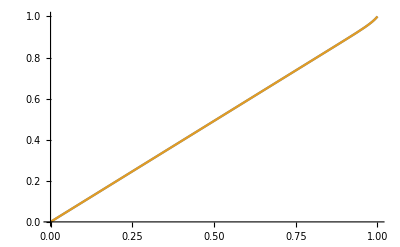

```mathematica
Plot[{CDF[𝒟, {u,u}],ClaytonCDF[u,u]}, {u,0,1}]
```

```mathematica
Simplify[ClaytonCDF[q,q]/q]
```

1/((2/q^40-1)^(1/40) q)

```mathematica
Simplify[CDF[𝒟,{q,q}]/q, Assumptions->0<q<1]
```

1/((2-q^40)^(1/40))

```mathematica
QD[q_?NumericQ]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
QD2[q_?NumericQ]:=
If[0<q≤0.5, ClaytonCDF[q,q]/q,(1-2q+ ClaytonCDF[q,q])/(1-q)]
```

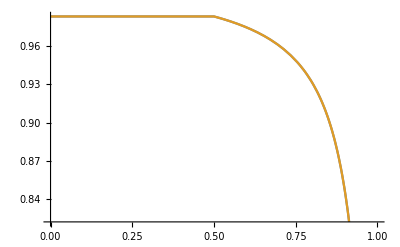

```mathematica
Plot[{QD[q],QD2[q]}, {q,0,1}]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
kk=18;
```

```mathematica
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
```

```mathematica
Clear[c, QD,𝒟]
```

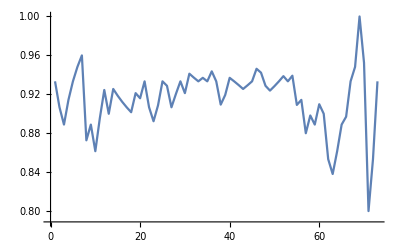

```mathematica
ListPlot[Table[QDemp[q, u, v], {q,0.05,0.95, 0.0125}],Joined->True]
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
QD[q_]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
target=Table[QDemp[q, u, v], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[target, KendallTau[u,v]];
target
```

{0.933333,0.933333,1.,0.933333,0.884563}

```mathematica
f= Table[QD[q], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[f, c/(c+2)]; (* Kendall's tau *)
Sqrt[Total[(target-f)^2]]
```

√((0.933333-20. (2 0.05^-c-1)^(-1/c))^2+(0.933333-10. (2 0.1^-c-1)^(-1/c))^2+(1.-10. ((2 0.9^-c-1)^(-1/c)-0.8))^2+(0.933333-20. ((2 0.95^-c-1)^(-1/c)-0.9))^2+(0.884563-c/(c+2))^2)

```mathematica
NMinimize[{Sqrt[Total[(target-f)^2]], c>0}, c]
```

{0.141561,{c→181.081}}

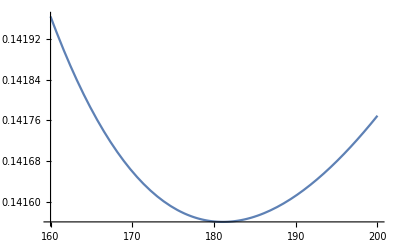

```mathematica
Plot[Sqrt[Total[(target-f)^2]], {c,160,200}]
```